## Searching for Eigenvalues

### Functions I used

This is the FindEigenvalues function, which returns the lowest eigenvalue and the number of negatives. I return both to check for when one of the lowest eigenvalues falls off.

```mathematica
FindEigenvalues[λ_]:=Module[{H,dρ,ρinf,nn,vals,neg,i},
dρ=0.1;
ρinf=λ*20;
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
vals=Sort[Eigenvalues[H,-100]];
neg=0;
For[i=1, vals[[i]]<0,i++,
neg++;
];
Print["Found eigenvalues for λ="<>ToString[λ]];
Return[{vals[[1]],neg}]
]
```

Initializing to make returning things easier.

```mathematica
res={};
val=FindEigenvalues[10];
vaf=FindEigenvalues[1000];
```

The function doing the actual work. It works recursively (like bisection), taking in a lower and upper bound and the lowest eigenvalue / number of negatives. I look for ranges where (a) the lowest eigenvalue at the high end is higher than the lowest eigenvalue at the low end (read: an eigenvalue fell off) ORr (b) the number of negatives increases (read: extra bound state wooo). I check both of these, because it’d be possible to lose a negative and gain a new one in a range and not be able to tell the difference.

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam},
mid=l0+(lf-l0)/2;
vam=FindEigenvalues[mid];
If[lf-l0>range,
If[val[[1]] < vam[[1]] ||val[[2]]<vam[[2]],
FindLs[l0,mid,val,vam,range];
];
If[vam[[1]] < vaf[[1]] || vam[[2]] < vaf[[2]],
FindLs[mid,lf,vam,vaf,range];
];,
res=Append[res,{l0,lf}];
Print["Found one!"];
]
]
```

#### This ran overnight and took a while

```mathematica
FindLs[10.,1000.,val,vaf,1]
```

Found one!

Found one!

Found one!

«54 more identical outputs»

### Results

I then took the results and returned the eigenvalues/negatives at each end of the range, just to check and see if FindLs did the right thing. There were 57 candidates found in the range λ=10 to λ=1000, which seemed large.

```mathematica
thing=Table[{FindEigenvalues[res[[i,1]]],FindEigenvalues[res[[i,2]]]},{i,1,Length[res]}]
```

Found eigenvalues for λ=12.9004

Found eigenvalues for λ=13.8672

Found eigenvalues for λ=15.8008

Found eigenvalues for λ=16.7676

Found eigenvalues for λ=19.668

Found eigenvalues for λ=20.6348

Found eigenvalues for λ=28.3691

Found eigenvalues for λ=29.3359

Found eigenvalues for λ=35.1367

Found eigenvalues for λ=36.1035

Found eigenvalues for λ=39.0039

Found eigenvalues for λ=39.9707

Found eigenvalues for λ=50.6055

Found eigenvalues for λ=51.5723

Found eigenvalues for λ=55.4395

Found eigenvalues for λ=56.4063

Found eigenvalues for λ=64.1406

Found eigenvalues for λ=65.1074

Found eigenvalues for λ=77.6758

Found eigenvalues for λ=78.6426

Found eigenvalues for λ=78.6426

Found eigenvalues for λ=79.6094

Found eigenvalues for λ=96.0449

Found eigenvalues for λ=97.0117

Found eigenvalues for λ=101.846

Found eigenvalues for λ=102.813

Found eigenvalues for λ=113.447

Found eigenvalues for λ=114.414

Found eigenvalues for λ=127.949

Found eigenvalues for λ=128.916

Found eigenvalues for λ=133.75

Found eigenvalues for λ=134.717

Found eigenvalues for λ=155.02

Found eigenvalues for λ=155.986

Found eigenvalues for λ=155.986

Found eigenvalues for λ=156.953

Found eigenvalues for λ=178.223

Found eigenvalues for λ=179.189

Found eigenvalues for λ=184.99

Found eigenvalues for λ=185.957

Found eigenvalues for λ=202.393

Found eigenvalues for λ=203.359

Found eigenvalues for λ=215.928

Found eigenvalues for λ=216.895

Found eigenvalues for λ=228.496

Found eigenvalues for λ=229.463

Found eigenvalues for λ=249.766

Found eigenvalues for λ=250.732

Found eigenvalues for λ=255.566

Found eigenvalues for λ=256.533

Found eigenvalues for λ=284.57

Found eigenvalues for λ=285.537

Found eigenvalues for λ=285.537

Found eigenvalues for λ=286.504

Found eigenvalues for λ=315.508

Found eigenvalues for λ=316.475

Found eigenvalues for λ=320.342

Found eigenvalues for λ=321.309

Found eigenvalues for λ=348.379

Found eigenvalues for λ=349.346

Found eigenvalues for λ=359.014

Found eigenvalues for λ=359.98

Found eigenvalues for λ=382.217

Found eigenvalues for λ=383.184

Found eigenvalues for λ=398.652

Found eigenvalues for λ=399.619

Found eigenvalues for λ=417.988

Found eigenvalues for λ=418.955

Found eigenvalues for λ=440.225

Found eigenvalues for λ=441.191

Found eigenvalues for λ=454.727

Found eigenvalues for λ=455.693

Found eigenvalues for λ=483.73

Found eigenvalues for λ=484.697

Found eigenvalues for λ=493.398

Found eigenvalues for λ=494.365

Found eigenvalues for λ=529.17

Found eigenvalues for λ=530.137

Found eigenvalues for λ=533.037

Found eigenvalues for λ=534.004

Found eigenvalues for λ=574.609

Found eigenvalues for λ=575.576

Found eigenvalues for λ=575.576

Found eigenvalues for λ=576.543

Found eigenvalues for λ=618.115

Found eigenvalues for λ=619.082

Found eigenvalues for λ=623.916

Found eigenvalues for λ=624.883

Found eigenvalues for λ=663.555

Found eigenvalues for λ=664.521

Found eigenvalues for λ=674.189

Found eigenvalues for λ=675.156

Found eigenvalues for λ=709.961

Found eigenvalues for λ=710.928

Found eigenvalues for λ=726.396

Found eigenvalues for λ=727.363

Found eigenvalues for λ=757.334

Found eigenvalues for λ=758.301

Found eigenvalues for λ=779.57

Found eigenvalues for λ=780.537

Found eigenvalues for λ=807.607

Found eigenvalues for λ=808.574

Found eigenvalues for λ=834.678

Found eigenvalues for λ=835.645

Found eigenvalues for λ=858.848

Found eigenvalues for λ=859.814

Found eigenvalues for λ=891.719

Found eigenvalues for λ=892.686

Found eigenvalues for λ=911.055

Found eigenvalues for λ=912.021

Found eigenvalues for λ=949.727

Found eigenvalues for λ=950.693

Found eigenvalues for λ=965.195

Found eigenvalues for λ=966.162

Here it is in TableForm, so you can see the pairs. Looking through this, I saw that some of the pairs had a lower number of negatives at the high bound, meaning either that only an eigenvalue was dropped, or that two eigenvalues were dropped and one was added.

```mathematica
TableForm[thing,TableDepth->1]
```

{{-0.851083,3},{-0.860757,4}}
{{-0.87672,4},{-0.149512,3}}
{{-0.162143,3},{-0.165683,4}}
{{-0.186267,4},{-0.188156,5}}
{{-0.197496,5},{-0.0648536,4}}
{{-0.0677231,4},{-0.0686033,5}}
{{-0.0763761,5},{-0.0769452,6}}
{{-0.0790475,6},{-0.0336201,5}}
{{-0.0364767,5},{-0.0367954,6}}
{{-0.0403333,6},{-0.0197873,5}}
{{-0.0197873,5},{-0.019978,6}}
{{-0.0227583,6},{-0.0228985,7}}
{{-0.0235676,7},{-0.0126681,6}}
{{-0.0137621,6},{-0.0138541,7}}
{{-0.0150292,7},{-0.00861162,6}}
{{-0.0089268,6},{-0.00898794,7}}
{{-0.0101428,7},{-0.0101922,8}}
{{-0.0101922,8},{-0.00612421,7}}
{{-0.00696462,7},{-0.00699951,8}}
{{-0.00720341,8},{-0.00448349,7}}
{{-0.00493864,7},{-0.00496392,8}}
{{-0.00527847,8},{-0.00338002,7}}
{{-0.00361099,7},{-0.00362959,8}}
{{-0.00399869,8},{-0.0026248,7}}
{{-0.00269552,7},{-0.00270948,8}}
{{-0.00308907,8},{-0.00206809,7}}
{{-0.00206809,7},{-0.00207867,8}}
{{-0.00237869,8},{-0.00238814,9}}
{{-0.00242558,9},{-0.00164996,8}}
{{-0.00186558,8},{-0.00187294,9}}
{{-0.0019453,9},{-0.00134311,8}}
{{-0.00148111,8},{-0.00148692,9}}
{{-0.00157786,9},{-0.00110288,8}}
{{-0.00119292,8},{-0.00119755,9}}
{{-0.00129687,9},{-0.000916511,8}}
{{-0.000969535,8},{-0.000973269,9}}
{{-0.00107845,9},{-0.000769773,8}}
{{-0.000797285,8},{-0.000800317,9}}
{{-0.00090618,9},{-0.000652706,8}}
{{-0.000660181,8},{-0.000662665,9}}
{{-0.000763892,9},{-0.000766227,10}}
{{-0.000766227,10},{-0.000556159,9}}
{{-0.000641892,9},{-0.000643831,10}}
{{-0.000653488,10},{-0.000477722,9}}
{{-0.000543985,9},{-0.000545605,10}}
{{-0.000561706,10},{-0.000413363,9}}
{{-0.000463274,9},{-0.000464637,10}}
{{-0.000486261,10},{-0.000360076,9}}
{{-0.000396285,9},{-0.000397438,10}}
{{-0.000422569,10},{-0.000314591,9}}
{{-0.000342303,9},{-0.000343283,10}}
{{-0.000369483,10},{-0.00027647,9}}
{{-0.000296711,9},{-0.000297549,10}}
{{-0.000324902,10},{-0.000244289,9}}
{{-0.000258017,9},{-0.000258736,10}}
{{-0.000286499,10},{-0.000216317,9}}
{{-0.000225647,9},{-0.000226267,10}}

To separate these out, I made a list of all instances where the number of negatives decreased over the interval. I also tacked on the position in the list to make deletion easy.

```mathematica
stuff={};
```

```mathematica
For[i=1,i≤Length[thing],i++,
If[thing[[i,1,2]]>thing[[i,2,2]],
stuff=Append[stuff,{i,thing[[i]]}]
]
]
```

```mathematica
TableForm[stuff,TableDepth->1]
```

{2,{{-0.87672,4},{-0.149512,3}}}
{5,{{-0.197496,5},{-0.0648536,4}}}
{8,{{-0.0790475,6},{-0.0336201,5}}}
{10,{{-0.0403333,6},{-0.0197873,5}}}
{13,{{-0.0235676,7},{-0.0126681,6}}}
{15,{{-0.0150292,7},{-0.00861162,6}}}
{18,{{-0.0101922,8},{-0.00612421,7}}}
{20,{{-0.00720341,8},{-0.00448349,7}}}
{22,{{-0.00527847,8},{-0.00338002,7}}}
{24,{{-0.00399869,8},{-0.0026248,7}}}
{26,{{-0.00308907,8},{-0.00206809,7}}}
{29,{{-0.00242558,9},{-0.00164996,8}}}
{31,{{-0.0019453,9},{-0.00134311,8}}}
{33,{{-0.00157786,9},{-0.00110288,8}}}
{35,{{-0.00129687,9},{-0.000916511,8}}}
{37,{{-0.00107845,9},{-0.000769773,8}}}
{39,{{-0.00090618,9},{-0.000652706,8}}}
{42,{{-0.000766227,10},{-0.000556159,9}}}
{44,{{-0.000653488,10},{-0.000477722,9}}}
{46,{{-0.000561706,10},{-0.000413363,9}}}
{48,{{-0.000486261,10},{-0.000360076,9}}}
{50,{{-0.000422569,10},{-0.000314591,9}}}
{52,{{-0.000369483,10},{-0.00027647,9}}}
{54,{{-0.000324902,10},{-0.000244289,9}}}
{56,{{-0.000286499,10},{-0.000216317,9}}}

More initializing. I didn’t want to fiddle with returns.

```mathematica
resfinal=res;
```

```mathematica
bogus={};
```

Here is the function that I used to check whether these intervals were, in fact, places where only an eigenvalue was dropped. To check this, I look at the second-lowest eigenvalue at the low edge and compare it to the lowest eigenvalue at the high edge. That eigenvalue should be the same one, and should decrease slightly as λ increases.
This also took for-friggin’-ever to run.

```mathematica
For[i=1,i<=Length[stuff],i++,
dρ=0.1;
λ=res[[stuff[[i,1]],1]]; (*Set lambda to lower bound*)
ρinf=λ*20;
nn=Round[ρinf/dρ];
Print["Calculating for number "<>ToString[i]]; (*so I can track its progress*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
ev1=Sort[Eigenvalues[H,-100]]; (*calculate eigenvalues for that lambda*)
λ=res[[stuff[[i,1]],2]]; (*and again to higher bound, using the index of the problematic pair from stuff.*)
ρinf=λ*20;
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
ev2=Sort[Eigenvalues[H,-100]];
If[ev1[[2]]>ev2[[1]], (*Does the check*)
bogus=Append[bogus,{stuff[[i,1]]}];
]
]
```

Calculating for number 1

Calculating for number 2

Calculating for number 3

Calculating for number 4

Calculating for number 5

Calculating for number 6

Calculating for number 7

Calculating for number 8

Calculating for number 9

Calculating for number 10

Calculating for number 11

Calculating for number 12

Calculating for number 13

Calculating for number 14

Calculating for number 15

Calculating for number 16

Calculating for number 17

Calculating for number 18

Calculating for number 19

Calculating for number 20

Calculating for number 21

Calculating for number 22

Calculating for number 23

Calculating for number 24

Calculating for number 25

```mathematica
bogus
```

{{2},{5},{8},{10},{13},{15},{18},{20},{22},{24},{26},{29},{31},{33},{35},{37},{39},{42},{44},{46},{48},{50},{52},{54},{56}}

Interestingly, every single potentially bad pair was bad (which makes a certain amount of sense -- it’s unlikely that two eigenvalues will fall of at the same time. But I had to be sure).

```mathematica
Length[bogus]
```

25

### Punchline

Here are the ranges for the lambdas, with the bad ones removed. Counting the three below λ=10, that makes 35 critical values of lambda, about what we expect.

```mathematica
resfinal=Delete[resfinal,bogus]
```

{{12.9004,13.8672},{19.668,20.6348},{28.3691,29.3359},{39.0039,39.9707},{50.6055,51.5723},{64.1406,65.1074},{78.6426,79.6094},{96.0449,97.0117},{113.447,114.414},{133.75,134.717},{155.02,155.986},{178.223,179.189},{202.393,203.359},{228.496,229.463},{255.566,256.533},{285.537,286.504},{315.508,316.475},{348.379,349.346},{382.217,383.184},{417.988,418.955},{454.727,455.693},{493.398,494.365},{533.037,534.004},{574.609,575.576},{618.115,619.082},{663.555,664.521},{709.961,710.928},{757.334,758.301},{807.607,808.574},{858.848,859.814},{911.055,912.021},{965.195,966.162}}

```mathematica
Length[resfinal]
```

32

Ranges’ midpoints plotted. Really rough data, but it looks squareish. The fit isn’t that great, but whatever. Next step: bisect these ranges and get error bars.

```mathematica
rough=Table[resfinal[[i,1]]+(resfinal[[i,2]]-resfinal[[i,1]])/2,{i,1,Length[resfinal]}];
```

```mathematica
fit=FindFit[rough,a*x^2,a,x];
```

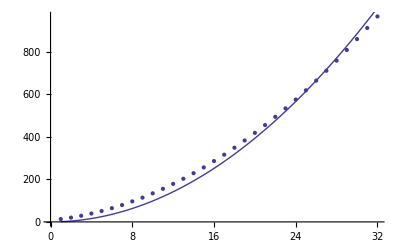

```mathematica
Show[ListPlot[rough],Plot[a*x^2/.fit,{x,1,Length[rough]}]]
```

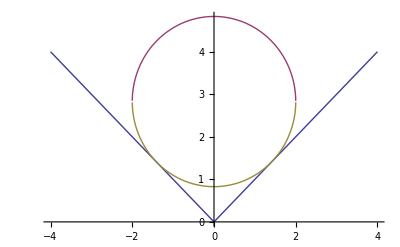

```mathematica
Plot[{Abs[x],Sqrt[4-x^2]+2 Sqrt[2],-Sqrt[4-x^2]+2 Sqrt[2]},{x,-4,4}]
```

(^ me being triumphant)